```mathematica
NormalizeData[symbol_,start_,end_]:=FinancialData[symbol,{start,end}]//Transpose@{#[[All,1]],#[[All,2]]/First@#[[All,2]]}&
PortfolioChart[stocks_,start_,end_]:=Module[{s,portfolio,data,symbols,std,return},
s=NormalizeData[#,start,end]&/@stocks;
portfolio=Transpose@{s[[1]][[All,1]],Mean/@Transpose@(#[[All,2]]&/@s)};
data=s~Join~{portfolio};
symbols=stocks~Join~{"portfolio"};
std=StandardDeviation@portfolio[[All,2]];
return=Last@portfolio[[All,2]];
{DateListPlot[data,PlotLegends->symbols,PlotTheme->"Detailed",ImageSize->Large,BaseStyle->{FontSize->20},PlotRange->All],{return,std,return/std}//TableForm[#,TableHeadings->{{"return","std","r/s"},Automatic}]&}
]
```

```mathematica
start=DatePlus[Today,-Quantity[5, "Years"]];
start1=DatePlus[Today,-Quantity[1, "Years"]];
start2=DatePlus[Today,-Quantity[2, "Years"]];
end=Today;
end//DateString
```

Tue 14 Mar 2017

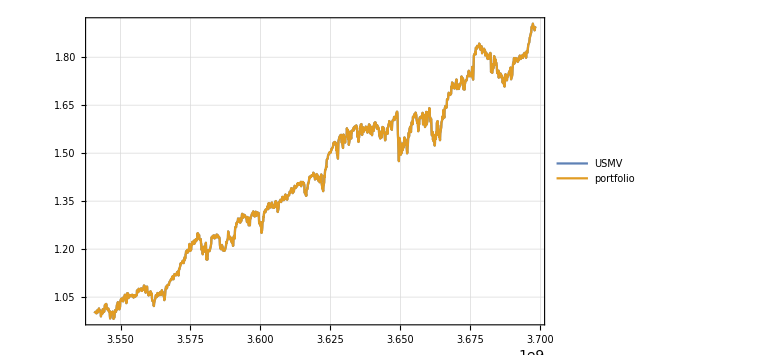
{-Graphics-,return | 1.89618
std | 0.25627
r/s | 7.39914}

```mathematica
PortfolioChart[{"USMV"},start,end]
```

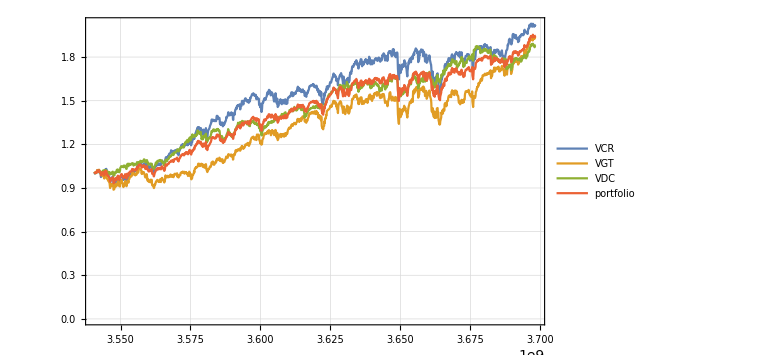
{-Graphics-,return | 1.94813
std | 0.274494
r/s | 7.09719}

```mathematica
PortfolioChart[{"VCR","VGT","VDC"},start,end]
```

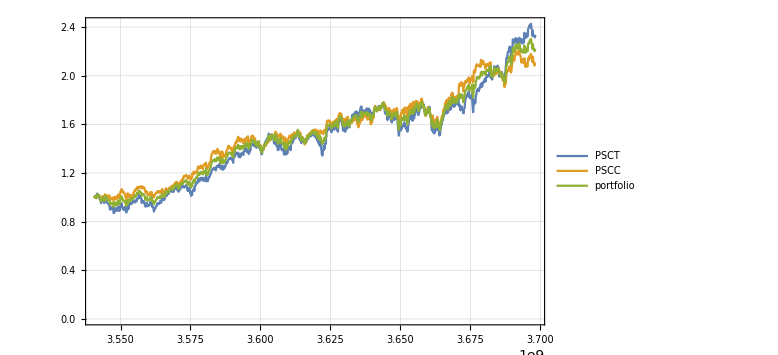
{-Graphics-,return | 2.21939
std | 0.355764
r/s | 6.23838}

```mathematica
PortfolioChart[{"PSCT","PSCC"},start,end]
```

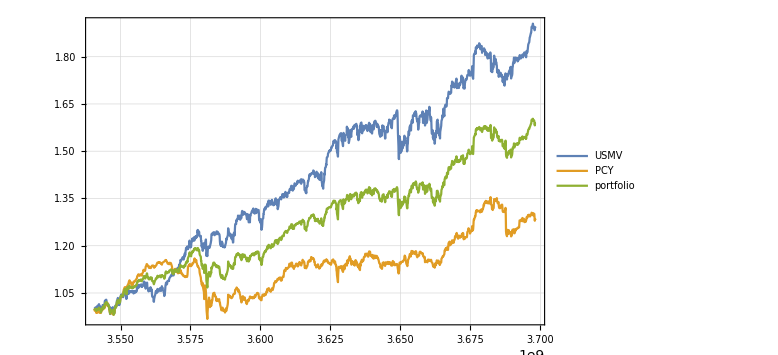
{-Graphics-,return | 1.58887
std | 0.165709
r/s | 9.58834}

```mathematica
PortfolioChart[{"USMV","PCY"},start,end]
```

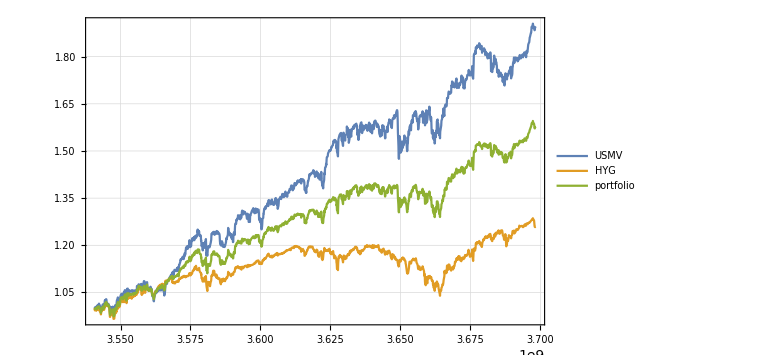
{-Graphics-,return | 1.57758
std | 0.157071
r/s | 10.0438}

```mathematica
PortfolioChart[{"USMV","HYG"},start,end]
```

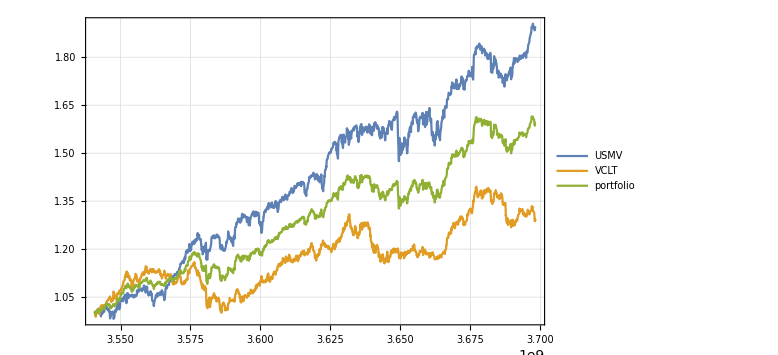
{-Graphics-,return | 1.59171
std | 0.17279
r/s | 9.21186}

```mathematica
PortfolioChart[{"USMV","VCLT"},start,end]
```

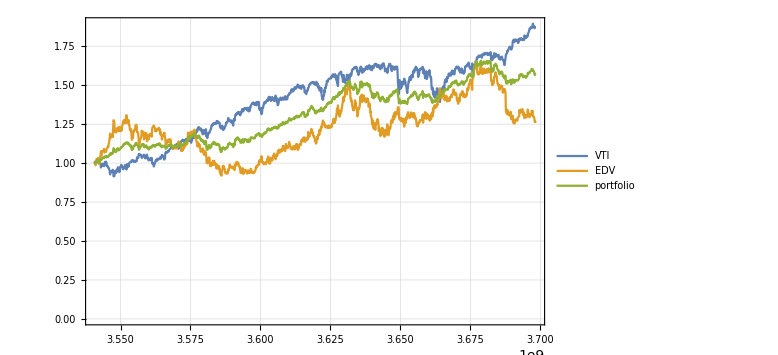
{-Graphics-,return | 1.56683
std | 0.185338
r/s | 8.45393}

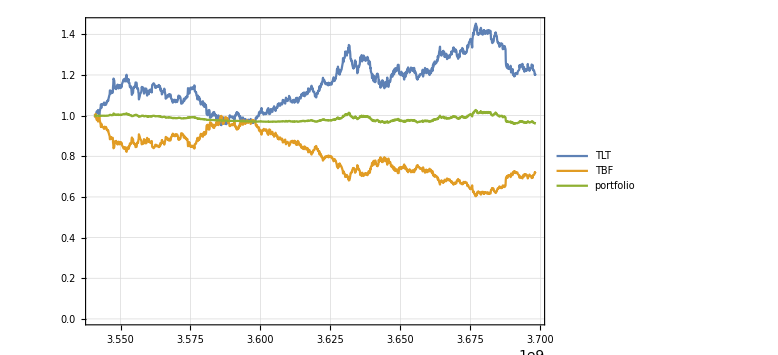
{-Graphics-,return | 0.960544
std | 0.0139148
r/s | 69.0302}

```mathematica
PortfolioChart[{"VTI","EDV"},start,end]
PortfolioChart[{"TLT","TBF"},start,end]
```

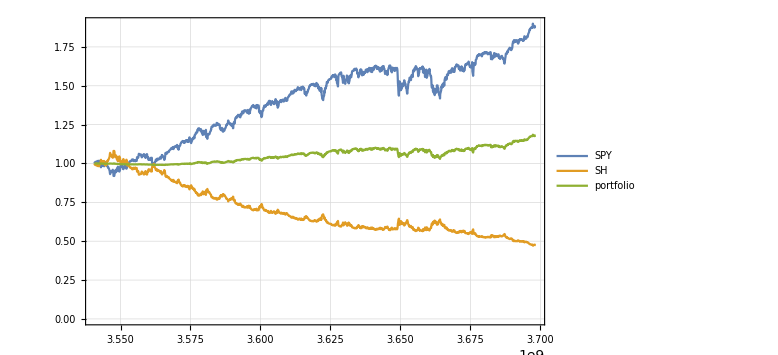
{-Graphics-,return | 1.17964
std | 0.0470618
r/s | 25.0657}

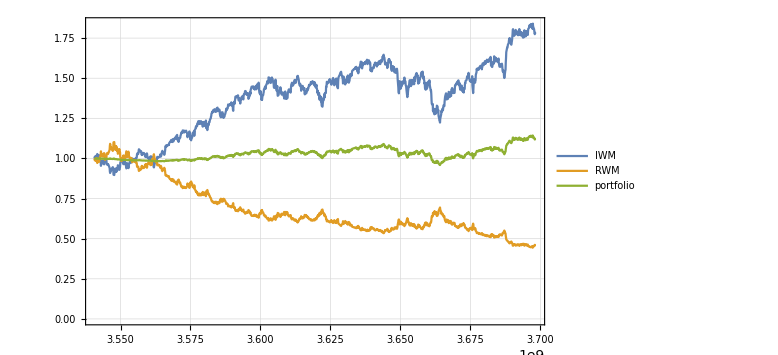
{-Graphics-,return | 1.12247
std | 0.0364915
r/s | 30.7598}

```mathematica
PortfolioChart[{"SPY","SH"},start,end]
PortfolioChart[{"IWM","RWM"},start,end]
```

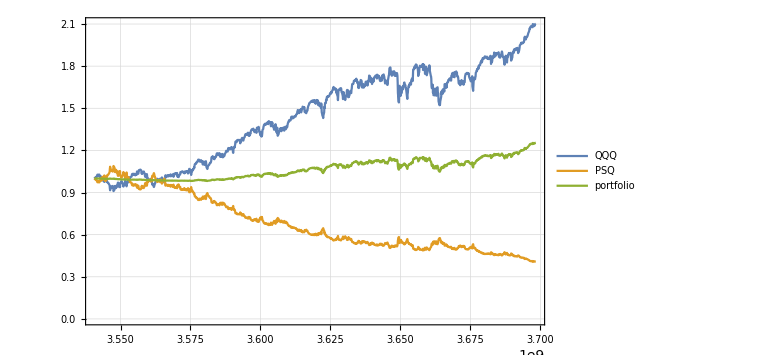
{-Graphics-,return | 1.25494
std | 0.0687505
r/s | 18.2535}

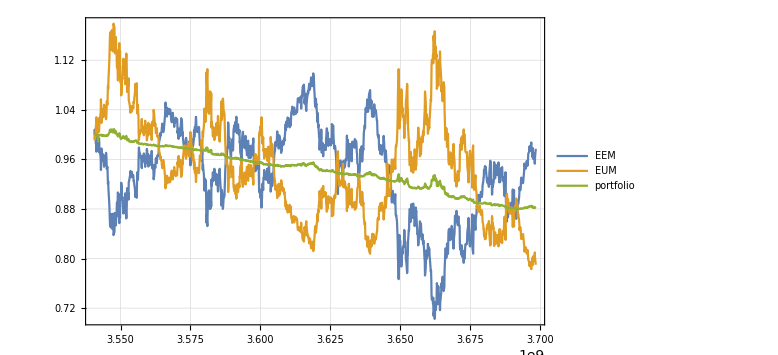
{-Graphics-,return | 0.883519
std | 0.0354443
r/s | 24.927}

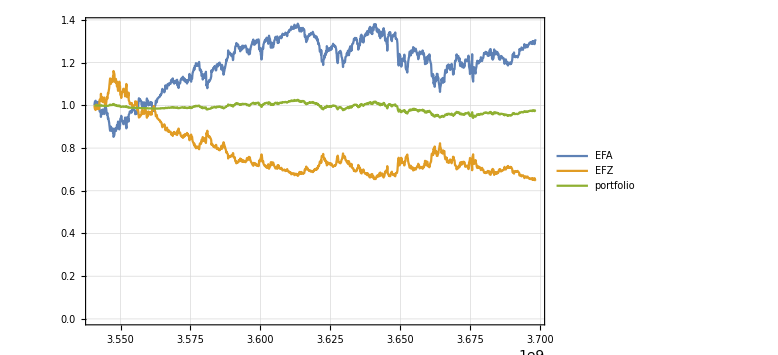
{-Graphics-,return | 0.978088
std | 0.0190864
r/s | 51.2452}

```mathematica
PortfolioChart[{"QQQ","PSQ"},start,end]
PortfolioChart[{"EEM","EUM"},start,end]
PortfolioChart[{"EFA","EFZ"},start,end]
```

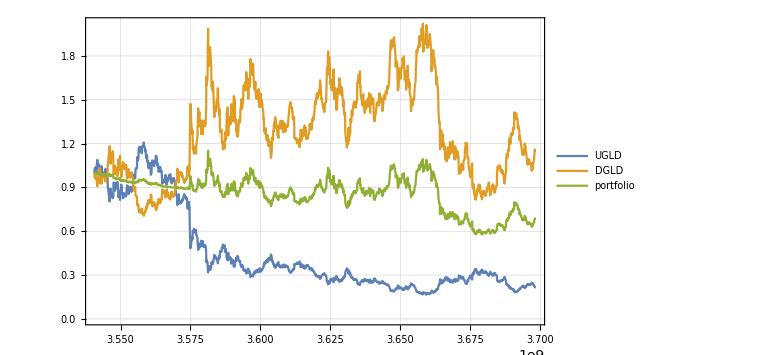
{-Graphics-,return | 0.685349
std | 0.119683
r/s | 5.72639}

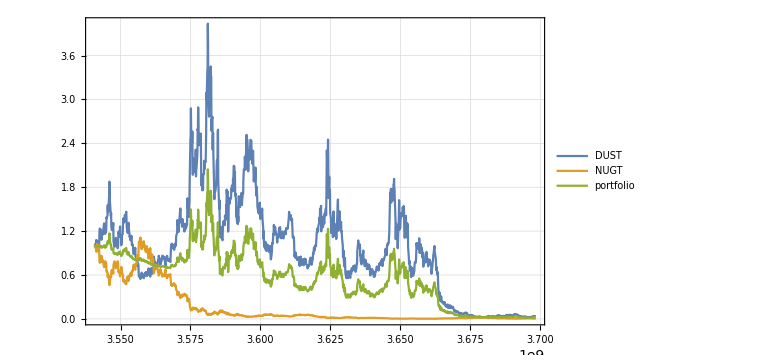
{-Graphics-,return | 0.0202593
std | 0.373393
r/s | 0.0542572}

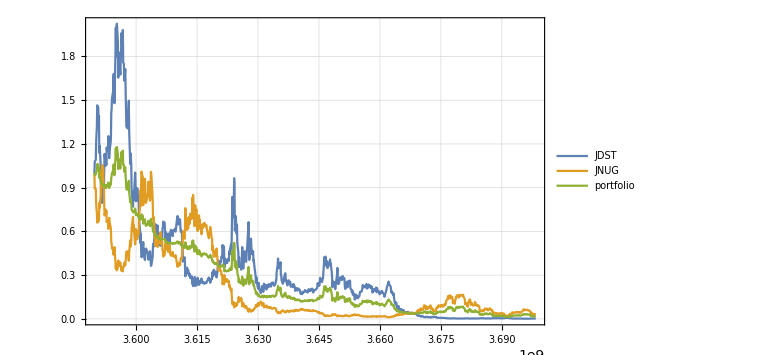
{-Graphics-,return | 0.0193394
std | 0.287658
r/s | 0.0672306}

```mathematica
PortfolioChart[{"UGLD","DGLD"},start,end]
PortfolioChart[{"DUST","NUGT"},start,end]
PortfolioChart[{"JDST","JNUG"},start,end]
```

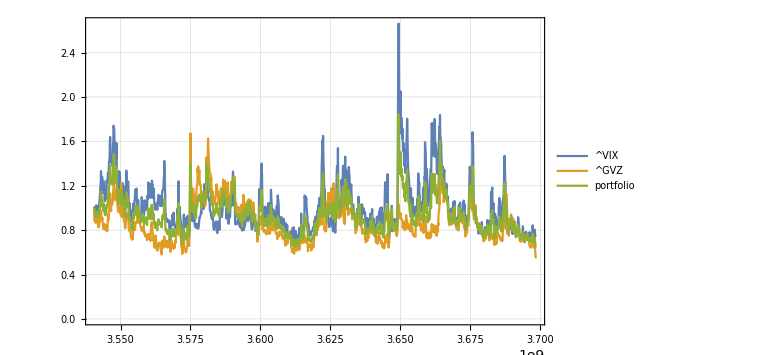
{-Graphics-,return | 0.644216
std | 0.161285
r/s | 3.99426}

```mathematica
PortfolioChart[{"^VIX","^GVZ"},start,end]
```